## NN Tunneling

```mathematica
a=CirclePoints[3];
(*Defined as in Haldane1988*)
latticepoints=Flatten[Table[{i,j,k}.CirclePoints[{√3,0},3]+#,{i,-1/2,1/2},{j,-1/2,1/2},{k,-1/2,1/2}]&/@CirclePoints[{1,π/2},6],3]//Union;
```

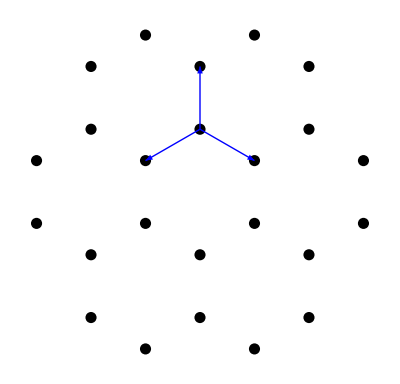

```mathematica
(*Show all NN hopping events involving one A site*)
Graphics[{
{Black,PointSize[0.02],Point[#]}&/@latticepoints,
{Blue,Arrow[{{0,1},{0,1}+#}]}&/@a
}]
```

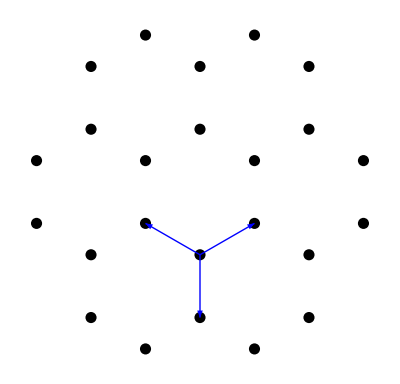

```mathematica
(*Show all NN hopping events involving one B site*)
Graphics[{
{Black,PointSize[0.02],Point[#]}&/@latticepoints,
{Blue,Arrow[{{0,-1},{0,-1}+#}]}&/@(-a)
}]
```

```mathematica
(*Sum up all hopping terms involving one A site*)
ABhopping=Total[Exp[I {kx,ky}.#]&/@a]//ComplexExpand
```

Cos[(√3 kx)/2-ky/2]+Cos[(√3 kx)/2+ky/2]+Cos[ky]+ⅈ (Sin[(√3 kx)/2-ky/2]-Sin[(√3 kx)/2+ky/2]+Sin[ky])

```mathematica
(*Compare to Haldane1988 paper expression*)
Total[Cos[{kx,ky}.#]&/@a]+I Total[Sin[{kx,ky}.#]&/@a]
```

Cos[(√3 kx)/2-ky/2]+Cos[(√3 kx)/2+ky/2]+Cos[ky]+ⅈ (Sin[(√3 kx)/2-ky/2]-Sin[(√3 kx)/2+ky/2]+Sin[ky])

```mathematica
(*Sum up all hopping terms involving one B site*)
BAhopping=Total[Exp[I {kx,ky}.#]&/@(-a)]//ComplexExpand
```

Cos[(√3 kx)/2-ky/2]+Cos[(√3 kx)/2+ky/2]+Cos[ky]+ⅈ (-Sin[(√3 kx)/2-ky/2]+Sin[(√3 kx)/2+ky/2]-Sin[ky])

```mathematica
(*Compare to Haldane1988 paper expression*)
Total[Cos[{kx,ky}.#]&/@a]-I Total[Sin[{kx,ky}.#]&/@a]
```

Cos[(√3 kx)/2-ky/2]+Cos[(√3 kx)/2+ky/2]+Cos[ky]-ⅈ (Sin[(√3 kx)/2-ky/2]-Sin[(√3 kx)/2+ky/2]+Sin[ky])

## NNN Tunneling

```mathematica
b=(#2-#1&@@@Partition[a,2,1,1]);(*Defined as in Haldane1988*)
```

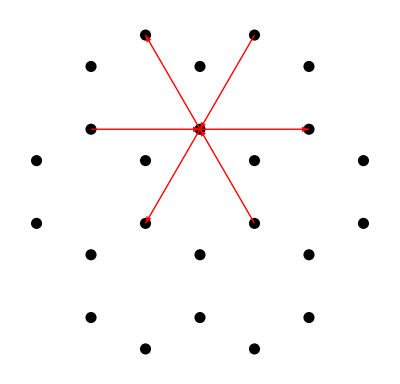

```mathematica
(*Show all NNN hopping events involving one A site*)
Graphics[{
{Black,PointSize[0.02],Point[#]}&/@latticepoints,
{Red,Arrow[#]}&/@Select[Flatten[Table[({i,j,k}.CirclePoints[{√3,0},3]+#ᵀ)ᵀ&/@Partition[CirclePoints[{1,π/2},3],2,1,1],{i,-1/2,1/2},{j,-1/2,1/2},{k,-1/2,1/2}],3]//Union,MemberQ[#,{0,1}]&]
}]
```

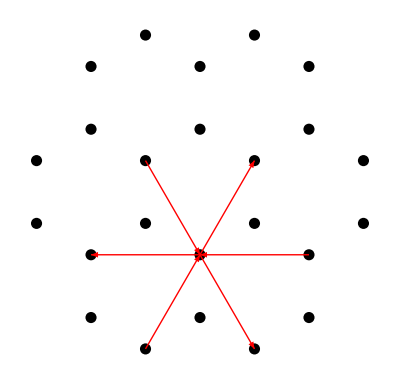

```mathematica
(*Show all NNN hopping events involving one B site*)
Graphics[{
{Black,PointSize[0.02],Point[#]}&/@latticepoints,
{Red,Arrow[#]}&/@Select[Flatten[Table[({i,j,k}.CirclePoints[{√3,0},3]+#ᵀ)ᵀ&/@Partition[CirclePoints[{1,-π/2},3],2,1,1],{i,-1/2,1/2},{j,-1/2,1/2},{k,-1/2,1/2}],3]//Union,MemberQ[#,{0,-1}]&]
}]
```

```mathematica
(*Sum up all hopping terms involving one A site while including alternate phases and simplify expression*)
Total[Exp[I {kx,ky}.#1+I #2 ϕ]&@@@({CirclePoints[{√3,0},6],Riffle[##]&@@(Table[#,3]&/@{1,-1})}ᵀ)]//FullSimplify
```

2 (Cos[1/2 (√3 kx-3 ky-2 ϕ)]+Cos[1/2 (√3 kx+3 ky-2 ϕ)]+Cos[√3 kx+ϕ])

```mathematica
(*Compare to Haldane1988 paper expression*)
2(Total[Cos[{kx,ky}.#]&/@b]Cos[ϕ]-Total[Sin[{kx,ky}.#]&/@b]Sin[ϕ])//FullSimplify
```

2 (Cos[1/2 (√3 kx-3 ky-2 ϕ)]+Cos[1/2 (√3 kx+3 ky-2 ϕ)]+Cos[√3 kx+ϕ])

```mathematica
(*Sum up all hopping terms involving one B site while including alternate phases and simplify expression*)
Total[Exp[I {kx,ky}.#1+I #2 ϕ]&@@@({CirclePoints[{√3,0},6],Riffle[##]&@@(Table[#,3]&/@{-1,1})}ᵀ)]//FullSimplify
```

2 (Cos[√3 kx-ϕ]+2 Cos[(3 ky)/2] Cos[(√3 kx)/2+ϕ])

```mathematica
(*Compare to Haldane1988 paper expression*)
2(Total[Cos[{kx,ky}.#]&/@b]Cos[ϕ]+Total[Sin[{kx,ky}.#]&/@b]Sin[ϕ])//FullSimplify
```

2 (Cos[√3 kx-ϕ]+2 Cos[(3 ky)/2] Cos[(√3 kx)/2+ϕ])

```mathematica
(*Verdict: When summing up the NNN hopping terms and making sure the sign of ϕ is chosen appropriately, we get the same result as in Haldane1988*)
```